# Assignment - 2

##### Om Gupta 214047

#### a)

```mathematica
eqn1a=D[y[x],{x,2}]+y[x]==0;
sol1a=DSolve[eqn1a,y[x],x]
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]}}

#### b)

```mathematica
eqn1b =D[y[x],{x,2}] -y[x]==0;
sol1b=DSolve[eqn1b,y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^-x C[2]}}

#### c)

```mathematica
eqn1c= D[y[x],{x,2}]-5D[y[x],x]+6y[x]==0;
sol1c=DSolve[eqn1c,y[x],x]
```

{{y[x]→ⅇ^(2 x) C[1]+ⅇ^(3 x) C[2]}}

#### d)

```mathematica
eqn1d =D[y[x],{x,2}]-5D[y[x],x]+6y[x]==Exp[x]+Exp[-x];
sol1d=DSolve[eqn1d,y[x],x]
```

```mathematica
{{y[x]->1/12 ⅇ^-x (1+6 ⅇ^(2 x))+ⅇ^(2 x) C[1]+ⅇ^(3 x) C[2]}}
```

#### Q2:

```mathematica
eqn2 =5D[y[x],{x,2}]-8D[y[x],x] +6y[x]==0;
sol2 =DSolve[eqn2,y[x],x]
```

{{y[x]→ⅇ^(4 x/5) C[2] Cos[(√14 x)/5]+ⅇ^(4 x/5) C[1] Sin[(√14 x)/5]}}

```mathematica
p2a1 = y[x]/.sol2/.{C[1]-> 1,C[2]->4};
```

```mathematica
{4 ⅇ^(4 x/5) Cos[(√14 x)/5]+ⅇ^(4 x/5) Sin[(√14 x)/5]}
```

{4 ⅇ^(4 x/5) Cos[(√14 x)/5]+ⅇ^(4 x/5) Sin[(√14 x)/5]}

```mathematica
p2a2 = y[x]/.sol2/.{C[1]->2,C[2]->3};
p2a3 = y[x] /.sol2 /.{C[1]->3,C[2]->6}
```

{6 ⅇ^(4 x/5) Cos[(√14 x)/5]+3 ⅇ^(4 x/5) Sin[(√14 x)/5]}

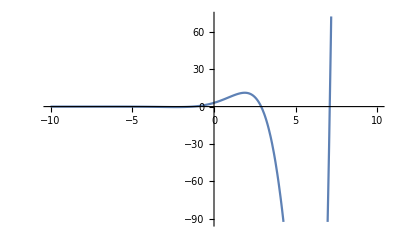

```mathematica
Plot[y[x]=ⅇ^(4x/5)3Cos[(√14 x)/5]+ⅇ^(4x/5)2Sin[(√14 x)/5], {x,-10,10}]
```

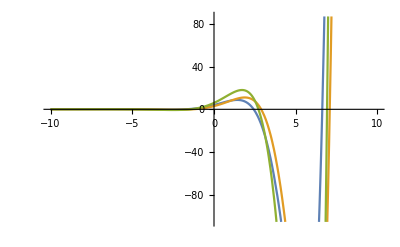

DSolve::deqn: Equation or list of equations expected instead of eqn1d in the first argument eqn1d.

```mathematica
Plot [{p2a1,p2a2,p2a3},{x,-10,10}]
```